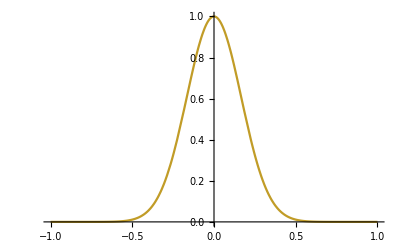

```mathematica
Plot[Exp[-1/2(x)^2/(1/36)],{x,-1,1}]
```

```mathematica
Series[Exp[-1/2(x)^2/(1/36)],{x,0,120}]
```

```mathematica
Reduce[1-18 x^2+162 x^4-972 x^6+4374 x^8-(78732 x^10)/5+(236196 x^12)/5<0,x]
```

False

```mathematica
Manipulate[Plot[Evaluate[Normal[Series[Exp[-1/2(x)^4/(1/36)],{x,0,a}]]],{x,-1,1}],{a,2,100,2}]
```

```mathematica
Select[Solve[Normal[Series[Exp[-1/2(x)^2/(1/36)],{x,0,92}]]==0,x],Im[#[[1,2]]]==0&]
```

{}

```mathematica
{x->-0.3159217749870583+1.3769526120333366 ⅈ}[[1,2]]
```

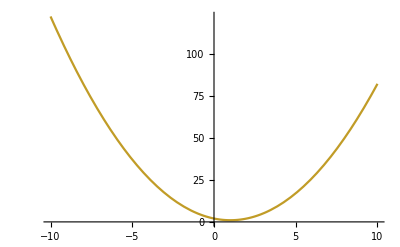

```mathematica
Plot[((x-1)^2+1),{x,-10,10}]
```

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
gauss=Exp[-(x-b)^2/(2c^2)]
gauss2=Exp[-(x)^2/(2)]
```

ⅇ^(-(-b+x)^2/(2 c^2))

ⅇ^(-x^2/2)

```mathematica
Table[D[gauss2,{x,i}]/i!/.x->0,{i,1,20}]
```

{0,-1/2,0,1/8,0,-1/48,0,1/384,0,-1/3840,0,1/46080,0,-1/645120,0,1/10321920,0,-1/185794560,0,1/3715891200}

```mathematica
Series[Exp[-x^2/2],{x,0,10}]
```

1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+O[x]^11

```mathematica
Table[D[gauss,{x,i}]/i!/.x->0,{i,1,20}]//Simplify
```

{(b ⅇ^(-b^2/(2 c^2)))/c^2,((b^2-c^2) ⅇ^(-b^2/(2 c^2)))/(2 c^4),(b (b^2-3 c^2) ⅇ^(-b^2/(2 c^2)))/(6 c^6),((b^4-6 b^2 c^2+3 c^4) ⅇ^(-b^2/(2 c^2)))/(24 c^8),(b (b^4-10 b^2 c^2+15 c^4) ⅇ^(-b^2/(2 c^2)))/(120 c^10),((b^6-15 b^4 c^2+45 b^2 c^4-15 c^6) ⅇ^(-b^2/(2 c^2)))/(720 c^12),(b (b^6-21 b^4 c^2+105 b^2 c^4-105 c^6) ⅇ^(-b^2/(2 c^2)))/(5040 c^14),((b^8-28 b^6 c^2+210 b^4 c^4-420 b^2 c^6+105 c^8) ⅇ^(-b^2/(2 c^2)))/(40320 c^16),(b (b^8-36 b^6 c^2+378 b^4 c^4-1260 b^2 c^6+945 c^8) ⅇ^(-b^2/(2 c^2)))/(362880 c^18),((b^10-45 b^8 c^2+630 b^6 c^4-3150 b^4 c^6+4725 b^2 c^8-945 c^10) ⅇ^(-b^2/(2 c^2)))/(3628800 c^20),(b (b^10-55 b^8 c^2+990 b^6 c^4-6930 b^4 c^6+17325 b^2 c^8-10395 c^10) ⅇ^(-b^2/(2 c^2)))/(39916800 c^22),((b^12-66 b^10 c^2+1485 b^8 c^4-13860 b^6 c^6+51975 b^4 c^8-62370 b^2 c^10+10395 c^12) ⅇ^(-b^2/(2 c^2)))/(479001600 c^24),(b (b^12-78 b^10 c^2+2145 b^8 c^4-25740 b^6 c^6+135135 b^4 c^8-270270 b^2 c^10+135135 c^12) ⅇ^(-b^2/(2 c^2)))/(6227020800 c^26),((b^14-91 b^12 c^2+3003 b^10 c^4-45045 b^8 c^6+315315 b^6 c^8-945945 b^4 c^10+945945 b^2 c^12-135135 c^14) ⅇ^(-b^2/(2 c^2)))/(87178291200 c^28),(b (b^14-105 b^12 c^2+4095 b^10 c^4-75075 b^8 c^6+675675 b^6 c^8-2837835 b^4 c^10+4729725 b^2 c^12-2027025 c^14) ⅇ^(-b^2/(2 c^2)))/(1307674368000 c^30),1/(20922789888000 c^32)(b^16-120 b^14 c^2+5460 b^12 c^4-120120 b^10 c^6+1351350 b^8 c^8-7567560 b^6 c^10+18918900 b^4 c^12-16216200 b^2 c^14+2027025 c^16) ⅇ^(-b^2/(2 c^2)),1/(355687428096000 c^34)b (b^16-136 b^14 c^2+7140 b^12 c^4-185640 b^10 c^6+2552550 b^8 c^8-18378360 b^6 c^10+64324260 b^4 c^12-91891800 b^2 c^14+34459425 c^16) ⅇ^(-b^2/(2 c^2)),1/(6402373705728000 c^36)(b^18-153 b^16 c^2+9180 b^14 c^4-278460 b^12 c^6+4594590 b^10 c^8-41351310 b^8 c^10+192972780 b^6 c^12-413513100 b^4 c^14+310134825 b^2 c^16-34459425 c^18) ⅇ^(-b^2/(2 c^2)),1/(121645100408832000 c^38)b (b^18-171 b^16 c^2+11628 b^14 c^4-406980 b^12 c^6+7936110 b^10 c^8-87297210 b^8 c^10+523783260 b^6 c^12-1571349780 b^4 c^14+1964187225 b^2 c^16-654729075 c^18) ⅇ^(-b^2/(2 c^2)),1/(2432902008176640000 c^40)(b^20-190 b^18 c^2+14535 b^16 c^4-581400 b^14 c^6+13226850 b^12 c^8-174594420 b^10 c^10+1309458150 b^8 c^12-5237832600 b^6 c^14+9820936125 b^4 c^16-6547290750 b^2 c^18+654729075 c^20) ⅇ^(-b^2/(2 c^2))}